## SFT calculations and asymptotics

This document explores and implements the exact integration of the Fourier transform on the ARM sphere of a simple but suitable model of a molecular orbital which works well for simple di- and tri-atomic molecules. The form factor R(p) of the ARM formalism can be expressed in terms of such a transform, which can be written as

            SFT(q)=∫dΩ/(2π)e^(-ⅈ q·r̂)F(r̂),
where F(r̂) is the angular part of the Dyson orbital, i.e. ⟨r|n_D⟩=C_κ κ^(3/2)(ⅇ^(-κ r)(κ r))^(Q/κ-1)F(r̂). This angular dependence can be modelled well, by all accounts, as

            F(r̂)=cosh(b cos θ)(1+c cos^2 θ)cos^N_z θ sin^(N_x+N_y)θ cos^N_x ϕ sin^N_y ϕ.

This model is taken from a paper by Ryan, Michael, Serguei and Misha (PRL 106 173001), and they in turn cite A.A. Radzig and B. M. Smirnov, Reference data on atoms, molecules and ions (Springer-Verlag, Berlin, 1985), as a source for that form. I have not been able to get that reference, though I suspect there’s a copy in MBI or nearby.

Anyway, as it turns out, this integral is exactly doable if you keep your analytical continuation wits about you, turn the cosh into exponentials, and you use a certain key formula (specifically, Gegenbauer’s finite integral, in Watson’s Bessel functions book, p. 50, or formulas 7.333.1 and .2 in Gradshteyn and Ryzhik). It comes out to the very nice form

            SFT(q)=(-ⅈ)^N_xyz∑_± (q_x^N_x(q_y^N_y(q_z±ⅈ b))^N_z)/((q_x^2+q_y^2+(q_z±ⅈ b)^2)^(N_xyz/2))[(1+c (N_z+1/2)/(N_xyz+3/2))j_N_xyz(√(q_x^2+q_y^2+(q_z±ⅈ b)^2))-c((q_z±ⅈ b)^2/(q_x^2+q_y^2+(q_z±ⅈ b)^2)-(N_z+1/2)/(N_xyz+3/2))j_(N_xyz+2)(√(q_x^2+q_y^2+(q_z±ⅈ b)^2))],
            
where the js are spherical Bessel functions and N_xyz=N_x+N_y+N_z.

One curious feature is that SFT(q) is only a function of the transverse momentum. This is because, by definition, q=a(p+A(t_s)), and t_s itself is a function of the momentum, through the saddle-point equation 1/2(p+A(t_s))+I_p=0, which can also be written as p_∥+A(t_s)=-ⅈ √(κ^2+p_⊥^2), and therefore q=a(p_⊥-ⅈ √(κ^2+p_⊥^2)n̂).


This document also contains some derived functions which help make sense of this solution.
   •  An approximation to SFT in the case of large a and small tunnelling angles. This can be further refined if necessary, but for now I left it in the form
 SFT(q)≃(-ⅈ)^N_xyz ⅇ^(κ a)/(κ a)(v_x/κ)^nx(v_y/κ)^ny ⅇ^(1/2(1-(κ^2+p_⊥^2)/κ^2 cos^2 θ)b^2/(κ a))1/2∑_± [(v_z/κ± ⅈ b/(κ a))^nz ⅇ^(∓ ⅈ b(-p_o/κsin θ -ⅈ(√(κ^2+p_⊥^2))/κ cos θ))(1-(N_xyz+1)/2(1-(N_xyz+3)(κ^2+p_⊥^2)/κ^2 cos^2 θ)b^2/(κ^2 a^2)± ⅈ (N_xyz+1) b/(κ a)(-p_o/κsin θ-ⅈ(√(κ^2+p_⊥^2))/κ cos θ))((1+c(N_z+1/2)/(N_xyz+3/2))-c ((v_z/κ± ⅈ b/(κ a))^2(1-(1-4(κ^2+p_⊥^2)/κ^2 cos^2 θ)b^2/(κ^2 a^2)± ⅈ 2 b/(κ a)(-po/κsin θ-ⅈ (√(κ^2+p_⊥^2))/κ cos θ))+(N_z+1/2)/(N_xyz+3/2)))].
 This is important because it displays the correct asymptotics with respect to a, as ⅇ^(κ a)/(κ a), which is needed to counteract the factor of κ a ⅇ^(-κ a) that comes from the spatial part of the orbital, as the complete form factor needs to be, at least approximately, independent of a. The exponential factor comes from the fact that the spherical Bessel functions are being taken at an argument which is close to √(q^2)≃√((-ⅈ κ a n̂)^2)≃√(-κ^2 a^2). This is imaginary, and therefore the Bessel functions are in the modified Bessel function regime. The branch cut on that square root does not matter, as it gets exactly canceled out by a corresponding branch cut in the denominator (q_x^2+q_y^2+(q_z±ⅈ b)^2)^(N_xyz/2), as long as both branch cuts are taken to be exactly the same. This is the case for the built-in functions in use in this implementation. Note here that the molecular axis is the z axis, and the laser is assumed to be in the (x,z) plane; p_o is the transverse momentum in that plane.
 
   • Restricted versions of SFT for the case of on-axis ionization, or slight variations. Specifically, there are simpler expressions available for the case of SFT(p_⊥=0), and for its derivatives with respect to p_o and p_ythere. These are useful because they can be used to approximate it as SFT(q)=SFT(p_⊥=0)+q_o∂/(∂q_o)SFT|_(p_⊥=0)+q_y∂/(∂q_y)SFT|_(p_⊥=0), which is the corresponding version of the small-angle approximation that is given in the single-electron ARM paper (Torlina et al, PRA 86 043409).

## Definitions

### Preliminaries

This assigns the value 1 to the formally undefined expression 0^0, which in this context is always a special case of r^n for real r and integer n. However, it is important to note that this is (in principle) dangerous, and it can potentially cause errors in other notebooks that are running on the same kernel.

```mathematica
Unprotect[Power];
Power[0,0]=1;
Power[0.+0.ⅈ,0]=1;
Power[0.,0]=1;
Protect[Power];
```

Some functions for support. The velocity vector vel at t_sas a function of alignment angle and transverse momentum and the corresponding q vector.

```mathematica
vel[θ_,po_,py_,κ_]:=(po{Cos[θ],0,-Sin[θ]}+py {0,1,0}-ⅈ √(κ^2+po^2+py^2){Sin[θ],0,Cos[θ]});
qvec[a_,θ_,po_,py_,κ_]:=a vel[θ,po,py,κ];
```

### SFTnumeric

Uses parallelized memoization as per mm.se/q/1259

```mathematica
SFTnumeric[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=With[{result=SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]},(SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]=result)/;result=!=Null];
SFTnumeric[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=SFTnumericParallelized[qx,qy,qz,b,c,nx,ny,nz]=SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]=NIntegrate[
1/(2π)ⅇ^(-ⅈ(qx Sin[θ]Cos[ϕ]+qy Sin[θ]Sin[ϕ]+qz Cos[θ]))Cosh[b Cos[θ]](1+c Cos[θ]^2)Cos[θ]^nz Sin[θ]^(nx+ny+1)Cos[ϕ]^nx Sin[ϕ]^ny
,{θ,0,π},{ϕ,0,2π}
,Method->"MultidimensionalRule"
]
SetSharedFunction[SFTnumericParallelized];
SFTnumeric[{qx_,qy_,qz_},b_,c_,nx_,ny_,nz_]:=SFTnumeric[qx,qy,qz,b,c,nx,ny,nz]
```

### SFTanalytic

```mathematica
SFTanalytic[qx_,qy_,qz_,b_,c_,nx_,ny_,nz_]:=With[{ss=Function[s,√(qx^2+qy^2+(qz+s ⅈ b)^2)],j=SphericalBesselJ,n=nx+ny+nz},
Sum[(-ⅈ)^(nx+ny+nz)qx^nx qy^ny(qz+s ⅈ b)^nz((1+c (nz+1/2)/(n+3/2))j[n,ss[s]]/ss[s]^n-c((qz+s ⅈ b)^2/(qx^2+qy^2+(qz+s ⅈ b)^2)-(nz+1/2)/(n+3/2))j[n+2,ss[s]]/ss[s]^n),{s,{1,-1}}]
]
SFTanalytic[{qx_,qy_,qz_},b_,c_,nx_,ny_,nz_]:=SFTanalytic[qx,qy,qz,b,c,nx,ny,nz]
```

### SFTasymptotic

#### AsymptoticBesselI

```mathematica
AsymptoticBesselI[n_,σ_,order_:1]:=Block[{n1,σ1},
AsymptoticBesselI[n1_,σ1_,order]=Normal[Delete[Series[BesselI[n1,σ1],{σ1,∞,order}],{2,2}]];
AsymptoticBesselI[n,σ,order]
]
```

This provides an appropriate asymptotic series for the spherical Bessel functions of the exact analytic SFT, which are in the modified-Bessel-function regime of the form j_n(ⅈ σ). 

It is important to note that the precise phrasing of this code is very important and it is overall very finicky.This is because the naive command for the asymptotic series of the Bessel function gets the polynomial part correctly, but it returns subexponential terms which are not desired and in general not particularly correct:

```mathematica
Series[BesselI[n,σ],{σ,∞,1}]
```

ⅇ^-σ (ⅇ^(2 σ) ((√(1/σ))/(√(2 π))+O[1/σ]^(3/2))+((ⅈ ⅇ^(ⅈ n π) √(1/σ))/(√(2 π))+O[1/σ]^(3/2)))

Leaving aside the weird factorization, the ⅇ^-σ ⅇ^(2σ) factor is correct but the pure exponential-decay factor in ⅇ^-σ×poly(σ) is not what we want for large σ. In some ways this is understandable as the half-integer modified Bessel functions come out in terms of hyperbolic sines and cosines,

```mathematica
BesselI[1/2,σ]
BesselI[11/2,σ]
```

(√(2/π) Sinh[σ])/(√σ)

((2+1890/σ^4+210/σ^2) Cosh[σ]+(-1890/σ^5-840/σ^3-30/σ) Sinh[σ])/(√(2 π) √σ)

but in the asymptotic regime these go away, and they are explicitly ignored in e.g. DLMF 10.40.1. Moreover, it is apparently impossible to get Mathematica to produce the asymptotic series without those terms, even by providing suitable Assumptions. To deal with this the code uses a Delete statement on the offending terms, but that relies on the to-be-deleted terms being in part ⟦2,2⟧ of the outputof Series, which is liable to break if the output is reordered through whatever reason.

So: the above code as stated works, just be very careful with these things when modifying it.

#### SFTasymptotic

```mathematica
ClearAll[SFTasymptotic];
SFTasymptotic[poo_,pyy_,θθ_,bb_,cc_,κκ_,aa_,nx_,ny_,nz_,order_]:=Block[{po,py,θ,b,c,κ,a},
SFTasymptotic[po_,py_,θ_,b_,c_,κ_,a_,nx,ny,nz,order]=Block[
{n=nx+ny+nz,qx,qy,qz,σ,s,κa},
σ=κa √(1+b^2/κa^2-2s b/κa √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+2s ⅈ b/κa po/κ Sin[θ]);
{qx,qy,qz}={κa(po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ])/κ,κa py/κ,κa(-ⅈ √(po^2+py^2+κ^2) Cos[θ]-po Sin[θ])/κ};
ⅇ^(κ a)ExpToTrig[Sum[
Normal[Series[
(-ⅈ)^n ⅇ^-κa qx^nx qy^ny(qz+s ⅈ b)^nz √(π/2)((1+c (nz+1/2)/(n+3/2))AsymptoticBesselI[n+1/2,σ,order+1]/σ^(n+1/2)-c((qz+s ⅈ b)^2+(nz+1/2)/(n+3/2)σ^2)AsymptoticBesselI[n+5/2,σ,order+1]/σ^(n+5/2))
,{κa,∞,order+1}]]/.{κa->κ a}
,{s,{1,-1}}]]
];
SFTasymptotic[poo,pyy,θθ,bb,cc,κκ,aa,nx,ny,nz,order]
]
```

### SFTrestricted

## Benchmarking

### SFTnumeric vs SFTanalytic

#### Pre-computation of SFTnumeric values

```mathematica
LaunchKernels[16];
```

```mathematica
Column@AbsoluteTiming@Block[{b=2.5,c=1,nx=0,ny=0,nz=0, part=Re[ⅇ^ⅈ#]&},
ParallelTable[
part[SFTnumeric[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15,1},{qz,-15,15,1}
]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

About 300s=5min on Ramanujan.

```mathematica
AbsoluteTiming[Block[{b=2.5,c=1,nx=0,ny=0,nz=0},
ParallelTable[
SFTnumeric[qx,0,qz,b,c,nx,ny,nz]
,{qx,-15,15,1},{qz,-15,15,1}
]
]⟦1;;5,1;;5⟧]
```

```mathematica
Save["~/Work/Scratch/data 17.03 numerical SFT integration.txt",SFTnumeric]
```

To recover

```mathematica
<<"~/Work/Scratch/data 17.03 numerical SFT integration.txt"
```

#### SFTnumeric vs SFTanalytic

```mathematica
Block[{b=2.5,c=1,nx=0,ny=0,nz=0, part=Re[ⅇ^ⅈ#]&},
Show[{
Plot3D[
part[SFTanalytic[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15},{qz,-15,15}
,PlotRange->Full
,PlotPoints->50
,ImageSize->500
],
DiscretePlot3D[
part[SFTnumeric[qx,0,qz,b,c,nx,ny,nz]]
,{qx,-15,15,1},{qz,-15,15,1}
,Filling->None
,PlotStyle->Black
]
}]
]
```

-Graphics3D-

### SFTanalytic vs SFTasymptotic

#### Precomputation ofasymptotics

```mathematica
Table[  AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]
(*re-run to check memoization*)
Table[  AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]
```

{{{{{2.33811,{0,0,0,0}},{3.52959,{0,0,0,1}},{5.94723,{0,0,0,2}}},{{2.93044,{0,0,1,0}},{4.55546,{0,0,1,1}},{9.45347,{0,0,1,2}}}},{{{2.88167,{0,1,0,0}},{4.34909,{0,1,0,1}},{8.28129,{0,1,0,2}}},{{3.60642,{0,1,1,0}},{5.93972,{0,1,1,1}},{12.1271,{0,1,1,2}}}}},{{{{2.94624,{1,0,0,0}},{4.48779,{1,0,0,1}},{8.93201,{1,0,0,2}}},{{3.73377,{1,0,1,0}},{6.17458,{1,0,1,1}},{13.0961,{1,0,1,2}}}},{{{3.66129,{1,1,0,0}},{5.85139,{1,1,0,1}},{10.5276,{1,1,0,2}}},{{6.32087,{1,1,1,0}},{10.3875,{1,1,1,1}},{19.0367,{1,1,1,2}}}}}}

{{{{{0.000262,{0,0,0,0}},{0.001337,{0,0,0,1}},{0.003363,{0,0,0,2}}},{{0.000214,{0,0,1,0}},{0.001584,{0,0,1,1}},{0.004476,{0,0,1,2}}}},{{{0.004894,{0,1,0,0}},{0.002131,{0,1,0,1}},{0.005241,{0,1,0,2}}},{{0.000535,{0,1,1,0}},{0.00148,{0,1,1,1}},{0.007515,{0,1,1,2}}}}},{{{{0.000218,{1,0,0,0}},{0.002018,{1,0,0,1}},{0.005381,{1,0,0,2}}},{{0.000277,{1,0,1,0}},{0.001667,{1,0,1,1}},{0.004562,{1,0,1,2}}}},{{{0.000217,{1,1,0,0}},{0.001384,{1,1,0,1}},{0.004262,{1,1,0,2}}},{{0.000279,{1,1,1,0}},{0.001877,{1,1,1,1}},{0.006671,{1,1,1,2}}}}}}

#### Asymptotics with a for fixed momentum

```mathematica
Column[Table[
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Labeled[Grid[Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,20},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]],Style["order="<>ToString[order],20],{Top,Left}]
]]]
,{order,0,2}],Spacings->Scaled[0.1]]
```

11.9295
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=0
26.6124
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=1
49.616
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=2

#### Long-range asymptotics for a fixed momentum.

```mathematica
Column[Table[
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Labeled[Grid[Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,100},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]],Style["order="<>ToString[order],20],{Top,Left}]
]]]
,{order,0,2}],Spacings->Scaled[0.1]]
```

11.9678
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=0
23.9256
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=1
45.9839
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-order=2

#### Other stuff

```mathematica
Block[{κ=1,c=1,b=2.5,θ=90°,part=Re[ⅇ^ⅈ#]&,nx=1,ny=0,nz=1,a=15},
Plot3D[
Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"]
,{po,-2,2},{py,-5,5}
,PlotRange->Full
]
]
```

-Graphics3D-

```mathematica
Column[AbsoluteTiming[Block[{κ=1,c=1,b=2.5,po=0,py=0,part=Re[#]&},
Grid[Transpose[Flatten[Table[
Plot3D[
Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"]
,{a,1,20},{θ,0,π}
,ImageSize->500
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT(q) \n nx="<>ToString[nx]<>", ny="<>ToString[ny]<>", nz="<>ToString[nz]
,ViewPoint->{2,-1.7,Scaled[0.0005]}
,PlotRangePadding->None
,PlotTheme->"Classic"
,Ticks->{Automatic,
Join[{#,#}&/@Range[0,π,π/6],{#,"",{0.01,0}}&/@Range[0,π,π/24]]
,Automatic}
]
,{nx,{0,1}},{ny,{0}},{nz,{0,1}}],{1,2}]]]
]]]
```

3.68851
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

## Old stuff

#### SFTanalytic vs SFTasymptotic

```mathematica
Quit
```

```mathematica
Table[  AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]
(*re-run to check memoization*)
Table[  AbsoluteTiming[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order];{nx,ny,nz,order}]  ,{nx,0,1},{ny,0,1},{nz,0,1},{order,0,2}]
```

{{{{{2.33811,{0,0,0,0}},{3.52959,{0,0,0,1}},{5.94723,{0,0,0,2}}},{{2.93044,{0,0,1,0}},{4.55546,{0,0,1,1}},{9.45347,{0,0,1,2}}}},{{{2.88167,{0,1,0,0}},{4.34909,{0,1,0,1}},{8.28129,{0,1,0,2}}},{{3.60642,{0,1,1,0}},{5.93972,{0,1,1,1}},{12.1271,{0,1,1,2}}}}},{{{{2.94624,{1,0,0,0}},{4.48779,{1,0,0,1}},{8.93201,{1,0,0,2}}},{{3.73377,{1,0,1,0}},{6.17458,{1,0,1,1}},{13.0961,{1,0,1,2}}}},{{{3.66129,{1,1,0,0}},{5.85139,{1,1,0,1}},{10.5276,{1,1,0,2}}},{{6.32087,{1,1,1,0}},{10.3875,{1,1,1,1}},{19.0367,{1,1,1,2}}}}}}

{{{{{0.000262,{0,0,0,0}},{0.001337,{0,0,0,1}},{0.003363,{0,0,0,2}}},{{0.000214,{0,0,1,0}},{0.001584,{0,0,1,1}},{0.004476,{0,0,1,2}}}},{{{0.004894,{0,1,0,0}},{0.002131,{0,1,0,1}},{0.005241,{0,1,0,2}}},{{0.000535,{0,1,1,0}},{0.00148,{0,1,1,1}},{0.007515,{0,1,1,2}}}}},{{{{0.000218,{1,0,0,0}},{0.002018,{1,0,0,1}},{0.005381,{1,0,0,2}}},{{0.000277,{1,0,1,0}},{0.001667,{1,0,1,1}},{0.004562,{1,0,1,2}}}},{{{0.000217,{1,1,0,0}},{0.001384,{1,1,0,1}},{0.004262,{1,1,0,2}}},{{0.000279,{1,1,1,0}},{0.001877,{1,1,1,1}},{0.006671,{1,1,1,2}}}}}}

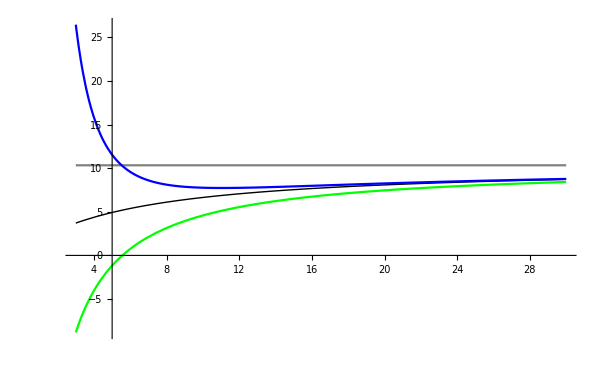

```mathematica
Block[{nx=0,ny=0,nz=0,order=1,κ=1,c=1,b=2.5,po=-0.5,py=0.15,θ=0°,part=Re[ⅇ^ⅈ#]&},
Plot[
Evaluate[Join[
{a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]]},
Table[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],{order,0,2}]
]]
,{a,3,30}
,ImageSize->600
,PlotRange->Full
,PlotStyle->{{Black,Thick},Gray,Green,Blue}
]
]
```

```mathematica
Block[{nx=0,ny=0,nz=0,order=0,κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,20},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
]
```

-Graphics3D-

-Graphics3D-

```mathematica
Column@AbsoluteTiming@Block[{order=2,κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,20},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]
]
```

50.3472
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

264.853
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
Column@AbsoluteTiming@Block[{order=1,κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,20},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]
]
```

27.0004
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

113.231
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
Column@AbsoluteTiming@Block[{order=0,κ=1,c=1,b=2.5,po=-0.5,py=0.15,part=Re[ⅇ^ⅈ#]&},
Transpose[Flatten[Table[
Plot3D[
{Tooltip[a ⅇ^(-κ a)part[SFTanalytic[qvec[a,θ,po,py,κ],b,c,nx,ny,nz]],"Analytic"],
Tooltip[a ⅇ^(-κ a)part[SFTasymptotic[po,py,θ,b,c,κ,a,nx,ny,nz,order]],"Asymptotic"]}
,{a,5,150},{θ,0,π}
,ImageSize->400
,AxesLabel->{"a","θ"}
,PlotLabel->"a ⅇ^-κaSFT \n nx="<>ToString[nx]<>" ny="<>ToString[ny]<>" nz="<>ToString[nz]
,ViewPoint->{2,-0.7,Scaled[0.0005]}
]
,{nx,{0,1}},{ny,{0,1}},{nz,{0,1}}],{1,2}]]
]
```

12.1586
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

45.5745
{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

```mathematica
SFTasymptotic[po,py,θ,b,c,κ,a,1,0,0,0]//Simplify//AbsoluteTiming
```

{0.30229,-(ⅈ ⅇ^(a κ) Cosh[(b (κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]-ⅈ po Sin[θ]))/κ] (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c (po^2+py^2+κ^2) Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2))/(a κ^4)}

```mathematica
{29.643259,1/(2 a^2 κ^8 √((po^2+py^2+κ^2)/κ^2))ⅇ^(a κ) (ⅈ po Cos[θ]+√(po^2+py^2+κ^2) Sin[θ]) (1/4 Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (c py^2+2 κ^2+c κ^2+c (2 po^2+py^2+κ^2) Cos[2 θ]-2 ⅈ c po √(po^2+py^2+κ^2) Sin[2 θ]) (κ √((po^2+py^2+κ^2)/κ^2) (-4 a κ^3+b^2 (py^2-κ^2))+b^2 κ √((po^2+py^2+κ^2)/κ^2) (2 po^2+py^2+κ^2) Cos[2 θ]-2 ⅈ b^2 po (po^2+py^2+κ^2) Sin[2 θ])+2 b κ^2 √((po^2+py^2+κ^2)/κ^2) ((2 κ^3 √((po^2+py^2+κ^2)/κ^2)+c (-2 po^2 (√(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))+κ (-2 κ √(po^2+py^2+κ^2)+3 py^2 √((po^2+py^2+κ^2)/κ^2)+3 κ^2 √((po^2+py^2+κ^2)/κ^2)))) Cos[θ]+c (κ (py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+2 po^2 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2))) Cos[3 θ]-2 ⅈ po (c py^2+κ^2+2 c κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+c (2 po^2+py^2+κ^2+2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)) Cos[2 θ]) Sin[θ]) Sinh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])}
```

Note the big red a where there’s supposed to be no a dependence in an order=0 expansion. This needs more work.

### Re-testing the asymptotics

```mathematica
(*ClearAll[SFTasymptotic];*)
(*SFTasymptotic[poo_,pyy_,θθ_,bb_,cc_,κκ_,aa_,nx_,ny_,nz_,order_]:=*)Block[{po,py,θ,b,c,κ,a},
(*SFTasymptotic[po_,py_,θ_,b_,c_,κ_,a_,nx,ny,nz,order]=*)Block[
{n=nx+ny+nz,qx,qy,qz,σ,s,κa,     nx=1,ny=0,nz=0,order=1},
σ=κa √(1+b^2/κa^2-2s b/κa √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+2s ⅈ b/κa po/κ Sin[θ]);
{qx,qy,qz}={κa(po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ])/κ,κa py/κ,κa(-ⅈ √(po^2+py^2+κ^2) Cos[θ]-po Sin[θ])/κ};
ⅇ^(κ a)ExpToTrig[Sum[
Normal[Series[
(-ⅈ)^n ⅇ^-κa qx^nx qy^ny(qz+s ⅈ b)^nz √(π/2)((1+c (nz+1/2)/(n+3/2))AsymptoticBesselI[n+1/2,σ,order+1]/σ^(n+1/2)-c((qz+s ⅈ b)^2+(nz+1/2)/(n+3/2)σ^2)AsymptoticBesselI[n+5/2,σ,order+1]/σ^(n+5/2))
,{κa,∞,order+1}]]/.{κa->κ a}
,{s,{1,-1}}]]
]
(*SFTasymptotic[poo,pyy,θθ,bb,cc,κκ,aa,nx,ny,nz,order]*)
]
Simplify[%]
a κ ⅇ^(-κ a)%
FreeQ[%,a]
```

ⅇ^(a κ) (1/(a^2 κ^2)(-1/(4 κ^3)ⅈ (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2) (b^2-1/4 (-2 b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+(2 ⅈ b po Sin[θ])/κ)^2) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]-Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])-1/κ ⅈ √(π/2) (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (-1/(√(2 π))-c/(5 √(2 π))+b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+1/5 b c √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b √(2/π) po Sin[θ])/κ-(ⅈ b c √(2/π) po Sin[θ])/(5 κ)+c (1/5 b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(b √(2/π) √(po^2+py^2+κ^2) Cos[θ])/κ+(4 ⅈ b √(2/π) po Sin[θ])/(5 κ)-((-3 √(2/π)+2 b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(2 ⅈ b √(2/π) po Sin[θ])/κ) (κ^2-5 po^2 Cos[θ]^2-5 py^2 Cos[θ]^2-5 κ^2 Cos[θ]^2+10 ⅈ po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]+5 po^2 Sin[θ]^2))/(5 κ^2))) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]-Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]))-1/(2 a κ^4)ⅈ (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]-Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])-1/(2 a κ^4)ⅈ (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]+Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])+1/(a^2 κ^2)(-1/(4 κ^3)ⅈ (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2) (b^2-1/4 (2 b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(2 ⅈ b po Sin[θ])/κ)^2) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]+Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])-1/κ ⅈ √(π/2) (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (-1/(√(2 π))-c/(5 √(2 π))-b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-1/5 b c √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+(ⅈ b √(2/π) po Sin[θ])/κ+(ⅈ b c √(2/π) po Sin[θ])/(5 κ)+c (-1/5 b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+(b √(2/π) √(po^2+py^2+κ^2) Cos[θ])/κ-(4 ⅈ b √(2/π) po Sin[θ])/(5 κ)-((-3 √(2/π)-2 b √(2/π) √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+(2 ⅈ b √(2/π) po Sin[θ])/κ) (κ^2-5 po^2 Cos[θ]^2-5 py^2 Cos[θ]^2-5 κ^2 Cos[θ]^2+10 ⅈ po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]+5 po^2 Sin[θ]^2))/(5 κ^2))) (Cosh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ]+Sinh[b √(1+po^2/κ^2+py^2/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])))

1/(2 a^2 κ^7)ⅇ^(a κ) (ⅈ po Cos[θ]+√(po^2+py^2+κ^2) Sin[θ]) (Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (b^2 c (po^2+py^2+κ^2)^2 Cos[θ]^4+(po^2+py^2+κ^2) Cos[θ]^2 (-2 c κ^2 (-6+a κ)+b^2 (κ^2-c (po^2+κ^2))+b^2 c po^2 Cos[2 θ])-2 ⅈ b^2 c po (po^2+py^2+κ^2) (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ]^3 Sin[θ]+po^2 κ^2 (b^2 (-1+c)+2 c (-6+a κ)) Sin[θ]^2+2 ⅈ b^2 c po^3 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ] Sin[θ]^3+b^2 c po^4 Sin[θ]^4-κ (κ^3 (b^2+2 (-1+c+a κ))-ⅈ po κ (2 c (-6+a κ) √(po^2+py^2+κ^2)+b^2 (c √(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))) Sin[2 θ]+b^2 c po^2 √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2) Sin[2 θ]^2))+2 b κ ((2 κ^3 √((po^2+py^2+κ^2)/κ^2)+c (-2 po^2 (√(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))+κ (-2 κ √(po^2+py^2+κ^2)+3 py^2 √((po^2+py^2+κ^2)/κ^2)+3 κ^2 √((po^2+py^2+κ^2)/κ^2)))) Cos[θ]+c (κ (py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+2 po^2 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2))) Cos[3 θ]-2 ⅈ po (c py^2+κ^2+2 c κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+c (2 po^2+py^2+κ^2+2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)) Cos[2 θ]) Sin[θ]) Sinh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])

1/(2 a κ^6)(ⅈ po Cos[θ]+√(po^2+py^2+κ^2) Sin[θ]) (Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (b^2 c (po^2+py^2+κ^2)^2 Cos[θ]^4+(po^2+py^2+κ^2) Cos[θ]^2 (-2 c κ^2 (-6+a κ)+b^2 (κ^2-c (po^2+κ^2))+b^2 c po^2 Cos[2 θ])-2 ⅈ b^2 c po (po^2+py^2+κ^2) (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ]^3 Sin[θ]+po^2 κ^2 (b^2 (-1+c)+2 c (-6+a κ)) Sin[θ]^2+2 ⅈ b^2 c po^3 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ] Sin[θ]^3+b^2 c po^4 Sin[θ]^4-κ (κ^3 (b^2+2 (-1+c+a κ))-ⅈ po κ (2 c (-6+a κ) √(po^2+py^2+κ^2)+b^2 (c √(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))) Sin[2 θ]+b^2 c po^2 √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2) Sin[2 θ]^2))+2 b κ ((2 κ^3 √((po^2+py^2+κ^2)/κ^2)+c (-2 po^2 (√(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))+κ (-2 κ √(po^2+py^2+κ^2)+3 py^2 √((po^2+py^2+κ^2)/κ^2)+3 κ^2 √((po^2+py^2+κ^2)/κ^2)))) Cos[θ]+c (κ (py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+2 po^2 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2))) Cos[3 θ]-2 ⅈ po (c py^2+κ^2+2 c κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+c (2 po^2+py^2+κ^2+2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)) Cos[2 θ]) Sin[θ]) Sinh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])

False

```mathematica
Series[(Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (b^2 c (po^2+py^2+κ^2)^2 Cos[θ]^4+(po^2+py^2+κ^2) Cos[θ]^2 (-2 c κ^2 (-6+a κ)+b^2 (κ^2-c (po^2+κ^2))+b^2 c po^2 Cos[2 θ])-2 ⅈ b^2 c po (po^2+py^2+κ^2) (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ]^3 Sin[θ]+po^2 κ^2 (b^2 (-1+c)+2 c (-6+a κ)) Sin[θ]^2+2 ⅈ b^2 c po^3 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ] Sin[θ]^3+b^2 c po^4 Sin[θ]^4-κ (κ^3 (b^2+2 (-1+c+a κ))-ⅈ po κ (2 c (-6+a κ) √(po^2+py^2+κ^2)+b^2 (c √(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))) Sin[2 θ]+b^2 c po^2 √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2) Sin[2 θ]^2))+2 b κ ((2 κ^3 √((po^2+py^2+κ^2)/κ^2)+c (-2 po^2 (√(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))+κ (-2 κ √(po^2+py^2+κ^2)+3 py^2 √((po^2+py^2+κ^2)/κ^2)+3 κ^2 √((po^2+py^2+κ^2)/κ^2)))) Cos[θ]+c (κ (py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+2 po^2 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2))) Cos[3 θ]-2 ⅈ po (c py^2+κ^2+2 c κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+c (2 po^2+py^2+κ^2+2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)) Cos[2 θ]) Sin[θ]) Sinh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])
,{a,0,4}]
```

(Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (2 κ^4-b^2 κ^4-2 c κ^4+b^2 c (po^2+py^2+κ^2)^2 Cos[θ]^4+(po^2+py^2+κ^2) Cos[θ]^2 (-b^2 c po^2+b^2 κ^2+12 c κ^2-b^2 c κ^2+b^2 c po^2 Cos[2 θ])-2 ⅈ b^2 c po (po^2+py^2+κ^2) (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ]^3 Sin[θ]+(-b^2-12 c+b^2 c) po^2 κ^2 Sin[θ]^2+2 ⅈ b^2 c po^3 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2)) Cos[θ] Sin[θ]^3+b^2 c po^4 Sin[θ]^4-12 ⅈ c po κ^2 √(po^2+py^2+κ^2) Sin[2 θ]+ⅈ b^2 c po κ^2 √(po^2+py^2+κ^2) Sin[2 θ]-ⅈ b^2 po κ^3 √((po^2+py^2+κ^2)/κ^2) Sin[2 θ]-b^2 c po^2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2) Sin[2 θ]^2)+2 b κ ((2 κ^3 √((po^2+py^2+κ^2)/κ^2)+c (-2 po^2 (√(po^2+py^2+κ^2)-κ √((po^2+py^2+κ^2)/κ^2))+κ (-2 κ √(po^2+py^2+κ^2)+3 py^2 √((po^2+py^2+κ^2)/κ^2)+3 κ^2 √((po^2+py^2+κ^2)/κ^2)))) Cos[θ]+c (κ (py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+2 po^2 (√(po^2+py^2+κ^2)+κ √((po^2+py^2+κ^2)/κ^2))) Cos[3 θ]-2 ⅈ po (c py^2+κ^2+2 c κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)+c (2 po^2+py^2+κ^2+2 κ √(po^2+py^2+κ^2) √((po^2+py^2+κ^2)/κ^2)) Cos[2 θ]) Sin[θ]) Sinh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ])+Cosh[b √((po^2+py^2+κ^2)/κ^2) Cos[θ]-(ⅈ b po Sin[θ])/κ] (-2 κ^5-2 c κ^3 (po^2+py^2+κ^2) Cos[θ]^2+2 c po^2 κ^3 Sin[θ]^2+2 ⅈ c po κ^3 √(po^2+py^2+κ^2) Sin[2 θ]) a+O[a]^5

```mathematica
(*ClearAll[SFTasymptotic];*)
(*SFTasymptotic[poo_,pyy_,θθ_,bb_,cc_,κκ_,aa_,nx_,ny_,nz_,order_]:=*)Block[{po,py,θ,b,c,κ,a},
(*SFTasymptotic[po_,py_,θ_,b_,c_,κ_,a_,nx,ny,nz,order]=*)Block[
{n=nx+ny+nz,qx,qy,qz,σ,s,κa,     nx=1,ny=0,nz=0,order=1},
σ=κa √(1+b^2/κa^2-2s b/κa √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+2s ⅈ b/κa po/κ Sin[θ]);
{qx,qy,qz}={κa(po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ])/κ,κa py/κ,κa(-ⅈ √(po^2+py^2+κ^2) Cos[θ]-po Sin[θ])/κ};
ⅇ^(κ a)ExpToTrig[Sum[
Normal[Series[
(-ⅈ)^n ⅇ^-κa qx^nx qy^ny(qz+s ⅈ b)^nz √(π/2)((1+c (nz+1/2)/(n+3/2))AsymptoticBesselI[n+1/2,σ,order+1]/σ^(n+1/2)-c((qz+s ⅈ b)^2+(nz+1/2)/(n+3/2)σ^2)AsymptoticBesselI[n+5/2,σ,order+1]/σ^(n+5/2))
,{κa,∞,order+1}]]/.{κa->κ a}
,{s,{1,-1}}]]
]
(*SFTasymptotic[poo,pyy,θθ,bb,cc,κκ,aa,nx,ny,nz,order]*)
]//Simplify;
Simplify[Series[a κ ⅇ^(-κ a)%,{a,∞,5}]]
```

```mathematica
Block[{po,py,θ,b,c,κ,a,       n=nx+ny+nz,qx,qy,qz,σ,s,κa,     nx=1,ny=0,nz=0,order=0},
σ=κa √(1+b^2/κa^2-2s b/κa √(1+po^2/κ^2+py^2/κ^2) Cos[θ]+2s ⅈ b/κa po/κ Sin[θ]);
{qx,qy,qz}={κa(po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ])/κ,κa py/κ,κa(-ⅈ √(po^2+py^2+κ^2) Cos[θ]-po Sin[θ])/κ};


Series[
(-ⅈ)^n ⅇ^-κa qx^nx qy^ny(qz+s ⅈ b)^nz √(π/2)((1+c (nz+1/2)/(n+3/2))AsymptoticBesselI[n+1/2,σ,order+1]/σ^(n+1/2)-c((qz+s ⅈ b)^2+(nz+1/2)/(n+3/2)σ^2)AsymptoticBesselI[n+5/2,σ,order+1]/σ^(n+5/2))
,{κa,∞,n+order+1}]

]
```

-(ⅈ ⅇ^(-b s √((po^2+py^2+κ^2)/κ^2) Cos[θ]+(ⅈ b po s Sin[θ])/κ) (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2))/(2 κ^3 κa)+1/κa^2(-1/(4 κ^3)ⅈ ⅇ^((-b s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]+ⅈ b po s Sin[θ])/κ) (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) (κ^2+c po^2 Cos[θ]^2+c py^2 Cos[θ]^2+c κ^2 Cos[θ]^2-2 ⅈ c po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]-c po^2 Sin[θ]^2) (b^2-1/4 (-2 b s √((po^2+py^2+κ^2)/κ^2) Cos[θ]+(2 ⅈ b po s Sin[θ])/κ)^2)-1/κ ⅈ ⅇ^((-b s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]+ⅈ b po s Sin[θ])/κ) √(π/2) (po Cos[θ]-ⅈ √(po^2+py^2+κ^2) Sin[θ]) ((5 b √(2/π) s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]+b c √(2/π) s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]-5 ⅈ b √(2/π) po s Sin[θ]-ⅈ b c √(2/π) po s Sin[θ])/(5 κ)+(c ((2 (-5 b s √(po^2+py^2+κ^2) Cos[θ]+b s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]+4 ⅈ b po s Sin[θ]))/(5 κ)-(4 (b s κ √((po^2+py^2+κ^2)/κ^2) Cos[θ]-ⅈ b po s Sin[θ]) (κ^2-5 po^2 Cos[θ]^2-5 py^2 Cos[θ]^2-5 κ^2 Cos[θ]^2+10 ⅈ po √(po^2+py^2+κ^2) Cos[θ] Sin[θ]+5 po^2 Sin[θ]^2))/(5 κ^3)))/(√(2 π))))+O[1/κa]^3